# Figures 2C(top), 2D(top), 2E(top), 2F(top), 3B(left), 4C, and S6

### This notebook generates the above figure panels . It used pre-processed data generated by process_ODs.nb

## Helper functions

```mathematica
SetDirectory[NotebookDirectory[]];

ksround=0.01; (* round-off parameters for the KS test for the least-frequent strain data *)

SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[DispPval]
DispPval[p_]:=Which[p<0.001,"<0.001",p<0.01,ToString[NumberForm[p,{2,4}]],p<0.1,ToString[NumberForm[p,{2,3}]],p<1,ToString[NumberForm[p,{2,2}]]]

SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram,BarChart,Graphics},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];

Clear[NaiveMinimization,testf]
NaiveMinimization[fun_,a0_,b0_,ϵ_]:=Module[{a,b,c,d,fa,fb,fc,fd,gr=1.(Sqrt[5]+1)/2},a=1.a0;b=1.b0;Do[
c=b-(b-a)/gr;
d=a+(b-a)/gr;
fa=fun[a];fb=fun[b];fc=fun[c];fd=fun[d];
If[fc<fd,b=d;fb=fd,a=c;fa=fc];
Print[a," ",b, " fa=",fc," fb=",fb];
If[(b-a)<ϵ,Break[]]
,{n,10}];
Return[(a+b)/2]]

Clear[FisherExactTest]
FisherExactTest[succ1_,n1_,succ2_,n2_]:=1.(n1! n2! (n1+n2-succ1-succ2)! (succ1+succ2)!)/((n1+n2)! (n1-succ1)! succ1! (n2-succ2)! succ2!)
```

## Data import and model parameters:

```mathematica
<<("turb_rif_long_runs_ODvsTIME_corrected.mx"); (* OD corrected for non-constant bkg and RIF contribution *)
dataRIFlong=data;
Length[dataRIFlong]

<<("turb_rif_long_runs.mx");
paramsRIFlong=alldata;

<<("turb_rif_short_runs.mx")
paramsRIFshort=alldata;

experfractions={0.4410869565217391,0.,0.,0.041666666666666664,0.12631578947368421,0.,0.,0.,0.,0.011004529709565681,0.,0.,0.40914897798742134,0.026738347859037517,0.015880348197421457,0.};
cfus={(* IChF *)31,15,30,7, (* 2022_06_14 *)   20,14,7,38,  (* 2022_02_24 *)  13,27,19,11 ,(* 2021_12_07*) 45,56,11,27 (* 2024_03_06 *)};

tmax=35;
odcrit=0.1;
odregrowth=0.05;
dilf=0.75;

(* for plotting and simulations *)
RIFlambda="0.16";RIF0="0.023"; (* values should be the same as in "process_ODs.nb" notebook *)
tregrowthbin={8,26,2};
tregrowthpmax=0.4;
cfusbin={0,80,5};
cfuspmax=0.05;
noreps="1000" ;(* number of replicate simulations *)
```

23

## Plotting functions

```mathematica
Clear[MakeBar2,MakeBarFromNM,RegrowthProbPlot,RegrowtTimeDistribution,LeastAbundantStrain]
MakeBar2[x_,y1_,y2_]:={AbsolutePointSize[10],Point[{x,(y1+y2)/2}],AbsoluteThickness[2],Line[{{x-0.25,y1},{x+0.25,y1}}],Line[{{x-0.25,y2},{x+0.25,y2}}],AbsoluteThickness[1],Line[{{x-0.15,y1},{x+0.15,y1}}],Line[{{x-0.15,y2},{x+0.15,y2}}],Line[{{x,y1},{x,y2}}]};
MakeBarFromNM[x_,n_,m_]:=MakeBar2[x,(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]]/.z->1 (* Wilson score interval https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval *)
RegrowthProbPlot[name_]:=Module[{gr,pval,pexp,pth,muypos},
pval=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
pexp=Length[Select[tregrowths,NumberQ[#1]&]]/Length[tregrowths];
pth=Length[Select[tmp,NumberQ[#1⟦2⟧]&]]/Length[tmp];
muypos=If[pexp>0.4 && pth>0.4,0.1,If[(pexp>0.5 && pth<0.5) || (pexp<0.5 && pth>0.5),0.5,1 ]];
gr=Graphics[{MakeBarFromNM[0.7,Length[tregrowths],Length[Select[tregrowths,NumberQ[#]&]]],Darker[Green],MakeBarFromNM[1.5,Length[tmp],Length[Select[tmp,(NumberQ[#[[2]]]&)]]]},(*Epilog->{Text["g_s",{0.7,0}],Text["g_r",{1.5,0}]},*)Axes->{None,Automatic},PlotRange->{{0,2},{0,1}},Axes->True,Frame->False,AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AspectRatio->1.3,ImageSize->200,PlotLabel->Style[("p_value= "<>DispPval[pval]),24],Epilog->(Style[Text[TextGrid[{{"μ="},{Read[StringToStream[mutrate],Number]}},Alignment->Center],{1,muypos}](*TextGrid[{{"μ=",Read[StringToStream[mutrate],Number]}}]*),24])];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"]]

RegrowtTimeDistribution[name_]:=Module[{gr,pval,grth,grexp},
grth=SmoothHistogram[Select[tmp,((NumberQ[#[[2]]])&)][[All,2]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],tregrowthbin,"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->200(*,ChartLegends->{"sim","exp"}*),PlotRange->{{tregrowthbin[[1]],tregrowthbin[[2]]},{0,tregrowthpmax}},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]]

LeastAbundantStrain[name_]:=Module[{fractions,gr},
If[Length[simdist[[1,1]]]==8,
fractions=Table[Min[1.#[[6]]/(#[[8]]+#[[6]]),1.#[[8]]/(#[[8]]+#[[6]])]&/@Select[simdist[[i]],(#[[6]]+#[[8]]>0)&],{i,Length[simdist]}]
,If[Length[simdist[[1,1]]]==10,fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}],Print["incorrect format"];Abort[]]];
gr=Histogram[{Flatten[fractions],experfractions},{0,0.5,0.1},"PDF",ScalingFunctions->{"Linear","Linear"},PlotRange->All,ChartStyle->{Darker[Green],Black},Frame->True,FrameTicks->{{{0,2,4,6,8},Automatic},{{0,0.25,0.5},Automatic}},FrameLabel->{"fraction",None(*"PDF"*)},ImageSize->200,(*ChartLegends->{"sim","exp"},*)AspectRatio->1,PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
Print["fraction below 0.1 (exp):",1.Length[Select[experfractions,(#<0.1)&]]/Length[experfractions]];
Print["fraction below 0.1 (sim):",1.Length[Select[Flatten[fractions],(#<0.1)&]]/Length[Flatten[fractions]]];
]

Clear[HistogramMutants]
HistogramMutants[namepart_,strains_,alleles_,output_,range_:{{0,cfusbin[[2]]},{0,cfuspmax}}]:=Module[{types=Table[Number,{strains*(alleles+1)}],simcfus,thcfus},
(* this simpler method ignores fitting the tfirstthr times, but works nevertheless and is much faster *)
simcfus=Table[ReadList[namepart<>ToString[n]<>".dat",types],{n,Length[births2]}];
Print[Length[simcfus]];
thcfus=Select[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],(#<=Max[cfus])&];
pl=Show[{Histogram[cfus,cfusbin,"PDF",ChartStyle->Gray],SmoothHistogram[thcfus,Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom,Frame->True,FrameLabel->{"n_r",None(*"PDF"*)},PlotRange->range]},PlotRange->range,AspectRatio->1,ImageSize->200,PlotLabel->Style[
"p_value= "<>DispPval[KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus]]
,24]];
Print[pl];
Export[output,pl,"PNG"]
]
```

### The fitting function that will be maximized when fitting the model to three data types:

```mathematica
Clear[FittingFunction]
FittingFunction[pval1_,pval2_,pval3_]:=pval1-If[pval2<0.1,100(0.1-pval2),0]-If[pval3<0.1,100(0.1-pval3),0]
```

## Simple model for RIF. Mixed strains AD30 and AD30YFP. One resistant allele.

### Long - term experiment

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsRIFlong;
Length[vols]
Do[If[birthsres[[i,1]]==0,tregrowths[[i]]=∞],{i,Length[births]}]
tregrowths
Print["mean time to regrowth = ",Max[Select[tregrowths,NumberQ]]]
Print["max. time to end = ",Max[Select[tends,NumberQ]]]
```

23

{20.8342,21.3245,19.9152,20.4595,19.2623,16.8407,17.8823,18.3482,19.7233,21.9101,21.8856,19.8833,19.8376,19.4321,22.3032,20.0352,24.7577,∞,17.3008,17.1475,21.71,14.9319,18.3095}

mean time to regrowth = 24.7577

max. time to end = 28.4733

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2.5 && Abs[#]>0)&])[[All,1,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,20,21,22,23}

### We use the same code as for the multi - allele model (see later sections), but select no . of alleles = 1:

```mathematica
mutrate="6.2e-9";  (* value from fluctuation test for AD30 and EEL02 *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\RIF\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}]]
```

6.2×10^-9

```mathematica
Export[NotebookDirectory[]<>"\\figures\\RIF_2_allele_no_lag_params.png",Style["μ="<>mutrate,FontSize->32],"PNG",ImageSize->300]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2_allele_no_lag_params.png

### This code runs the actual mode as parallel runs:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 23 13 fixed_mu_2strains_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_4.dat 0.1 fixed_mu_2strains_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_5.dat 0.1 fixed_mu_2strains_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_6.dat 0.1 fixed_mu_2strains_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_7.dat 0.1 fixed_mu_2strains_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_8.dat 0.1 fixed_mu_2strains_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_9.dat 0.1 fixed_mu_2strains_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_10.dat 0.1 fixed_mu_2strains_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_11.dat 0.1 fixed_mu_2strains_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_12.dat 0.1 fixed_mu_2strains_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_13.dat 0.1 fixed_mu_2strains_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_14.dat 0.1 fixed_mu_2strains_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_15.dat 0.1 fixed_mu_2strains_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_16.dat 0.1 fixed_mu_2strains_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_17.dat 0.1 fixed_mu_2strains_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_18.dat 0.1 fixed_mu_2strains_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_19.dat 0.1 fixed_mu_2strains_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_20.dat 0.1 fixed_mu_2strains_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_21.dat 0.1 fixed_mu_2strains_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_22.dat 0.1 fixed_mu_2strains_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_23.dat 0.1

0

0.98945

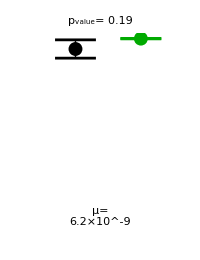

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2allele_no_lag_Pregrowth.png

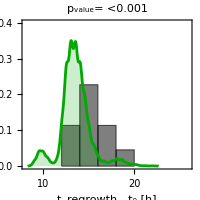

KS-test p-value: 1.97894×10^-6

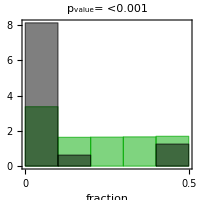

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.336923

```mathematica
simdist=Table[Import["models\\RIF\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["RIF_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["RIF_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["RIF_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
{vols2,births2,odinis2,tfirstthr2,tends2}=paramsRIFshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
odregrowth2=0.05;
```

16

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\RIF\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

6.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF"]
args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_RIF"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 16 13 preexist_res_2strains_1_allele_6.2e-9_RIF1 25.19 0.00398153 100 4.465 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF2 24.93 0.00349311 100 4.46503 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF3 24.01 0.00435082 100 4.46511 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF4 26.48 0.00390985 100 4.46514 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_4.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF5 25.41 0.00108037 100 5.614 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_5.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF6 24.82 0.000859569 100 5.61403 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_6.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF7 24.95 0.000998523 100 5.61408 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_7.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF8 26.22 0.000831875 100 5.61414 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_8.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF9 26.08 0.00502178 100 4.43167 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_9.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF10 24.92 0.0042102 100 4.43172 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_10.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF11 24.47 0.00456304 100 4.43178 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_11.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF12 25.58 0.004318 100 4.43183 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_12.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF13 25.28 0.00598778 100 4.39206 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_13.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF14 25.43 0.00487188 100 4.39211 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_14.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF15 24.44 0.00556088 100 4.39217 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_15.dat  0.1 preexist_res_2strains_1_allele_6.2e-9_RIF16 25.86 0.00500046 100 4.39222 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_16.dat  0.1

0

16

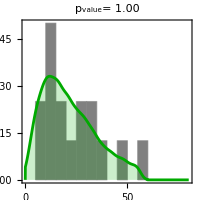

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\RIF\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_RIF",strains,alleles,NotebookDirectory[]<>"\\figures\\RIF_2allele_no_lag_Nmut.png"]
```

### Find the optimal mu that maximizes the p - value :

```mathematica
Clear[RunOnce,mu]
RunOnce[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\RIF"];

args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2]," 100 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)
simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus];
Return[-pval]]
```

```mathematica
RunOnce[6.2 10^-9]
```

-0.960535

```mathematica
NaiveMinimization[RunOnce,2 10^-9,10 10^-9,10^-10]
```

5.05573×10^-9 1.×10^-8 fa=-0.560242 fb=-0.00505112

5.05573×10^-9 8.11146×10^-9 fa=-0.572035 fb=-0.127163

5.05573×10^-9 6.94427×10^-9 fa=-0.961917 fb=-0.572035

5.05573×10^-9 6.22291×10^-9 fa=-0.962948 fb=-0.961917

5.50155×10^-9 6.22291×10^-9 fa=-0.911084 fb=-0.961917

5.77709×10^-9 6.22291×10^-9 fa=-0.962948 fb=-0.961917

5.94738×10^-9 6.22291×10^-9 fa=-0.96455 fb=-0.961917

5.94738×10^-9 6.11767×10^-9 fa=-0.983512 fb=-0.964445

6.01242×10^-9 6.11767×10^-9 fa=-0.982139 fb=-0.964445

6.01242×10^-9 6.07747×10^-9 fa=-0.983512 fb=-0.972499

6.04494×10^-9

#### This is almost exactly what came from the fluctuation test!

## Single - allele model for RIF. Phenotypic lag . Mixed strains AD30 and AD30YFP.

### Long - term experiment

```mathematica
mutrate="6.2e-9";  (* this value comes from the previous model and the fluctuation test result *)

lagrate="0.04" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.6; (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
mutprobs={1,1};
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* intermediate strains before and after the antibiotics*)
it={births[[nn,1]]{1,1},intgrfraction If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\RIF_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs,{"end"}],"Table"]
,{nn,Length[vols]}]]
```

6.2×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_lag"]
args=Table[
{"fixed_mu_2_strains_lag_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 23 14 fixed_mu_2_strains_lag_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_1.dat  0.1  0.04 fixed_mu_2_strains_lag_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_2.dat  0.1  0.04 fixed_mu_2_strains_lag_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_3.dat  0.1  0.04 fixed_mu_2_strains_lag_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_4.dat  0.1  0.04 fixed_mu_2_strains_lag_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_5.dat  0.1  0.04 fixed_mu_2_strains_lag_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_6.dat  0.1  0.04 fixed_mu_2_strains_lag_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_7.dat  0.1  0.04 fixed_mu_2_strains_lag_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_8.dat  0.1  0.04 fixed_mu_2_strains_lag_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_9.dat  0.1  0.04 fixed_mu_2_strains_lag_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_10.dat  0.1  0.04 fixed_mu_2_strains_lag_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_11.dat  0.1  0.04 fixed_mu_2_strains_lag_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_12.dat  0.1  0.04 fixed_mu_2_strains_lag_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_13.dat  0.1  0.04 fixed_mu_2_strains_lag_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_14.dat  0.1  0.04 fixed_mu_2_strains_lag_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_15.dat  0.1  0.04 fixed_mu_2_strains_lag_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_16.dat  0.1  0.04 fixed_mu_2_strains_lag_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_17.dat  0.1  0.04 fixed_mu_2_strains_lag_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_18.dat  0.1  0.04 fixed_mu_2_strains_lag_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_19.dat  0.1  0.04 fixed_mu_2_strains_lag_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_20.dat  0.1  0.04 fixed_mu_2_strains_lag_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_21.dat  0.1  0.04 fixed_mu_2_strains_lag_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_22.dat  0.1  0.04 fixed_mu_2_strains_lag_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_23.dat  0.1  0.04

0

0.939524

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2_allele_lag_params.png

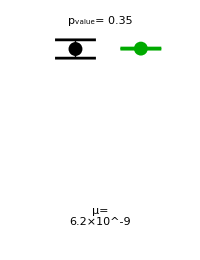

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2_allele_lag_Pregrowth.png

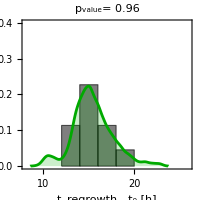

KS-test p-value: 0.957436

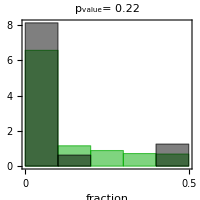

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.656533

```mathematica
simdist=Table[Import["models\\RIF_lag\\distribution_fixed_mu_2_strains_lag_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\RIF_2_allele_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["RIF_2_allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["RIF_2_allele_lag_Tregrowth.png"]
LeastAbundantStrain["RIF_2_allele_lag_LBS.png"]
```

### Find optimal parameters:

```mathematica
Clear[RunOnce1,ω,q]
mu=Interpreter["Number"][mutrate]
SeedRandom[1234]
RunOnce1[ω_?NumericQ,q_?NumericQ]:=RunOnce1[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
strains=2;alleles=1;
mutprobs={1,1}  ;(* same mutation probs for all alleles *)
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={births[[nn,1]]{1,1},Abs[q] If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\RIF_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs,{"end"}],"Table"]
,{nn,Length[vols]}];
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth]," 300 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",ToString[Abs[ω]]},{nn,Length[births]}]; (* tolerance, omega *)

name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];

ret=RunProcess[{"powershell",name}];

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\RIF_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

6.2×10^-9

RandomGeneratorState[…]

```mathematica
RunOnce1[0.05,0.5]
```

ω= 0.05 q =0.5 fun=-0.259059

-0.259059

```mathematica
fits=Table[{ω,q,RunOnce1[ω,q]},{ω,0.01,0.06,0.005},{q,0.4,0.9,0.1}]
```

ω= 0.01 q =0.4 fun=13.7417

ω= 0.01 q =0.5 fun=9.78878

ω= 0.01 q =0.6 fun=9.39584

ω= 0.01 q =0.7 fun=9.30009

ω= 0.01 q =0.8 fun=14.7632

ω= 0.01 q =0.9 fun=9.54501

ω= 0.015 q =0.4 fun=2.96586

ω= 0.015 q =0.5 fun=7.84911

ω= 0.015 q =0.6 fun=6.83107

ω= 0.015 q =0.7 fun=6.31857

ω= 0.015 q =0.8 fun=8.76755

ω= 0.015 q =0.9 fun=9.64163

ω= 0.02 q =0.4 fun=-0.00318965

ω= 0.02 q =0.5 fun=0.573967

ω= 0.02 q =0.6 fun=-0.238546

ω= 0.02 q =0.7 fun=0.242249

ω= 0.02 q =0.8 fun=8.90592

ω= 0.02 q =0.9 fun=9.69353

ω= 0.025 q =0.4 fun=-0.0119241

ω= 0.025 q =0.5 fun=-0.119683

ω= 0.025 q =0.6 fun=-0.257008

ω= 0.025 q =0.7 fun=3.81737

ω= 0.025 q =0.8 fun=8.90153

ω= 0.025 q =0.9 fun=12.2892

ω= 0.03 q =0.4 fun=-0.0221623

ω= 0.03 q =0.5 fun=-0.171264

ω= 0.03 q =0.6 fun=-0.316733

ω= 0.03 q =0.7 fun=5.13924

ω= 0.03 q =0.8 fun=9.05115

ω= 0.03 q =0.9 fun=12.0309

ω= 0.035 q =0.4 fun=-0.0416833

ω= 0.035 q =0.5 fun=-0.184795

ω= 0.035 q =0.6 fun=-0.359861

ω= 0.035 q =0.7 fun=5.56111

ω= 0.035 q =0.8 fun=9.20783

ω= 0.035 q =0.9 fun=18.2928

ω= 0.04 q =0.4 fun=-0.0617367

ω= 0.04 q =0.5 fun=-0.220882

ω= 0.04 q =0.6 fun=-0.362021

ω= 0.04 q =0.7 fun=6.29794

ω= 0.04 q =0.8 fun=9.39085

ω= 0.04 q =0.9 fun=19.3086

ω= 0.045 q =0.4 fun=-0.075

ω= 0.045 q =0.5 fun=-0.256732

ω= 0.045 q =0.6 fun=-0.357456

ω= 0.045 q =0.7 fun=6.93997

ω= 0.045 q =0.8 fun=9.32312

ω= 0.045 q =0.9 fun=19.2789

ω= 0.05 q =0.4 fun=-0.0891834

ω= 0.05 q =0.6 fun=-0.37436

ω= 0.05 q =0.7 fun=7.25117

ω= 0.05 q =0.8 fun=12.0857

ω= 0.05 q =0.9 fun=19.486

ω= 0.055 q =0.4 fun=-0.137717

ω= 0.055 q =0.5 fun=-0.303118

ω= 0.055 q =0.6 fun=-0.375244

ω= 0.055 q =0.7 fun=7.72949

ω= 0.055 q =0.8 fun=16.2235

ω= 0.055 q =0.9 fun=19.2868

ω= 0.06 q =0.4 fun=-0.155495

ω= 0.06 q =0.5 fun=-0.313659

ω= 0.06 q =0.6 fun=-0.376643

ω= 0.06 q =0.7 fun=7.73932

ω= 0.06 q =0.8 fun=16.1782

ω= 0.06 q =0.9 fun=19.5859

{{{0.01,0.4,13.7417},{0.01,0.5,9.78878},{0.01,0.6,9.39584},{0.01,0.7,9.30009},{0.01,0.8,14.7632},{0.01,0.9,9.54501}},{{0.015,0.4,2.96586},{0.015,0.5,7.84911},{0.015,0.6,6.83107},{0.015,0.7,6.31857},{0.015,0.8,8.76755},{0.015,0.9,9.64163}},{{0.02,0.4,-0.00318965},{0.02,0.5,0.573967},{0.02,0.6,-0.238546},{0.02,0.7,0.242249},{0.02,0.8,8.90592},{0.02,0.9,9.69353}},{{0.025,0.4,-0.0119241},{0.025,0.5,-0.119683},{0.025,0.6,-0.257008},{0.025,0.7,3.81737},{0.025,0.8,8.90153},{0.025,0.9,12.2892}},{{0.03,0.4,-0.0221623},{0.03,0.5,-0.171264},{0.03,0.6,-0.316733},{0.03,0.7,5.13924},{0.03,0.8,9.05115},{0.03,0.9,12.0309}},{{0.035,0.4,-0.0416833},{0.035,0.5,-0.184795},{0.035,0.6,-0.359861},{0.035,0.7,5.56111},{0.035,0.8,9.20783},{0.035,0.9,18.2928}},{{0.04,0.4,-0.0617367},{0.04,0.5,-0.220882},{0.04,0.6,-0.362021},{0.04,0.7,6.29794},{0.04,0.8,9.39085},{0.04,0.9,19.3086}},{{0.045,0.4,-0.075},{0.045,0.5,-0.256732},{0.045,0.6,-0.357456},{0.045,0.7,6.93997},{0.045,0.8,9.32312},{0.045,0.9,19.2789}},{{0.05,0.4,-0.0891834},{0.05,0.5,-0.259059},{0.05,0.6,-0.37436},{0.05,0.7,7.25117},{0.05,0.8,12.0857},{0.05,0.9,19.486}},{{0.055,0.4,-0.137717},{0.055,0.5,-0.303118},{0.055,0.6,-0.375244},{0.055,0.7,7.72949},{0.055,0.8,16.2235},{0.055,0.9,19.2868}},{{0.06,0.4,-0.155495},{0.06,0.5,-0.313659},{0.06,0.6,-0.376643},{0.06,0.7,7.73932},{0.06,0.8,16.1782},{0.06,0.9,19.5859}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.06,0.6,-0.376643},{0.055,0.6,-0.375244},{0.05,0.6,-0.37436},{0.04,0.6,-0.362021},{0.035,0.6,-0.359861},{0.045,0.6,-0.357456},{0.03,0.6,-0.316733},{0.06,0.5,-0.313659},{0.055,0.5,-0.303118},{0.05,0.5,-0.259059},{0.025,0.6,-0.257008},{0.045,0.5,-0.256732},{0.02,0.6,-0.238546},{0.04,0.5,-0.220882},{0.035,0.5,-0.184795},{0.03,0.5,-0.171264},{0.06,0.4,-0.155495},{0.055,0.4,-0.137717},{0.025,0.5,-0.119683},{0.05,0.4,-0.0891834},{0.045,0.4,-0.075},{0.04,0.4,-0.0617367},{0.035,0.4,-0.0416833},{0.03,0.4,-0.0221623},{0.025,0.4,-0.0119241},{0.02,0.4,-0.00318965},{0.02,0.7,0.242249},{0.02,0.5,0.573967},{0.015,0.4,2.96586},{0.025,0.7,3.81737},{0.03,0.7,5.13924},{0.035,0.7,5.56111},{0.04,0.7,6.29794},{0.015,0.7,6.31857},{0.015,0.6,6.83107},{0.045,0.7,6.93997},{0.05,0.7,7.25117},{0.055,0.7,7.72949},{0.06,0.7,7.73932},{0.015,0.5,7.84911},{0.015,0.8,8.76755},{0.025,0.8,8.90153},{0.02,0.8,8.90592},{0.03,0.8,9.05115},{0.035,0.8,9.20783},{0.01,0.7,9.30009},{0.045,0.8,9.32312},{0.04,0.8,9.39085},{0.01,0.6,9.39584},{0.01,0.9,9.54501},{0.015,0.9,9.64163},{0.02,0.9,9.69353},{0.01,0.5,9.78878},{0.03,0.9,12.0309},{0.05,0.8,12.0857},{0.025,0.9,12.2892},{0.01,0.4,13.7417},{0.01,0.8,14.7632},{0.06,0.8,16.1782},{0.055,0.8,16.2235},{0.035,0.9,18.2928},{0.045,0.9,19.2789},{0.055,0.9,19.2868},{0.04,0.9,19.3086},{0.05,0.9,19.486},{0.06,0.9,19.5859}}

```mathematica
ListPlot3D[Flatten[fits,1],PlotRange->{All,0},AxesLabel->{"ω","q","-p"}]
```

-Graphics3D-

### This clearly shows there is a large range of (ω, q) values that give good fits to data . We select one pair (0.035, 0.6) for which all p_values are much larger than 0.1

```mathematica
ListDensityPlot[Flatten[fits,1],PlotRange->{All,-0.05}]
```

-Graphics-

### Short - term experiment :

```mathematica
{vols2,births2,odinis2,tfirstthr2,tends2}=paramsRIFshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
```

16

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
wt={births2[[nn,1]]{1,1},{0,0}};
(* intermediate strains before and after the antibiotics*)
it={births2[[nn,1]]{1,1},intgrfraction births2[[nn,1]]{1,1}};
(* mutant strains before and after the antibiotic *)
mt={births2[[nn,1]]{1,1},births2[[nn,1]]{1,1}};
Export[NotebookDirectory[]<>"\\models\\RIF_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs,{"end"}],"Table"]
,{nn,Length[vols2]}]
```

6.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_lag"]

args=Table[
{"preexist_res_2_strains_lag_"<>mutrate<>"_RIF"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
Run["powershell "<>name]


SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 16 14 preexist_res_2_strains_lag_6.2e-9_RIF1 25.19 0.00398153 100 4.465 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_1.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF2 24.93 0.00349311 100 4.46503 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_2.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF3 24.01 0.00435082 100 4.46511 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_3.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF4 26.48 0.00390985 100 4.46514 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_4.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF5 25.41 0.00108037 100 5.614 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_5.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF6 24.82 0.000859569 100 5.61403 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_6.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF7 24.95 0.000998523 100 5.61408 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_7.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF8 26.22 0.000831875 100 5.61414 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_8.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF9 26.08 0.00502178 100 4.43167 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_9.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF10 24.92 0.0042102 100 4.43172 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_10.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF11 24.47 0.00456304 100 4.43178 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_11.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF12 25.58 0.004318 100 4.43183 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_12.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF13 25.28 0.00598778 100 4.39206 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_13.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF14 25.43 0.00487188 100 4.39211 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_14.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF15 24.44 0.00556088 100 4.39217 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_15.dat  0.1  0.04 preexist_res_2_strains_lag_6.2e-9_RIF16 25.86 0.00500046 100 4.39222 100 0.05 1000 6.200000000000001e-9 6.200000000000001e-9 0.75 input_params_16.dat  0.1  0.04

0

16

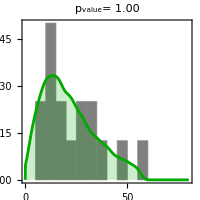

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_2_allele_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\RIF_lag\\strains_preexist_res_2_strains_lag_"<>mutrate<>"_RIF",strains,2alleles,NotebookDirectory[]<>"\\figures\\RIF_2_allele_lag_Nmut.png"]
```

## Multi-allele model for RIF. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];

allrates={"rpoB "<>#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&];
DumpSave[NotebookDirectory[]<>"\\RIF_mult_alleles.mx",allrates]

LBrates=allrates[[All,2]];
RIFrates=allrates[[All,3]];
LBrates
RIFrates

mutrate="8.3e-9";  (* this value has been chosen to give the best fit to CFUs data *)
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};

Export[NotebookDirectory[]<>"\\models\\RIF_mult\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}]]
```

{{{rpoB S512P,1.77465,1.43415},{rpoB S512F,1.80241,1.5536},{rpoB D516Y,1.99908,2.03764},{rpoB T563P,1.68159,0.76101},{rpoB H526Y,1.88764,1.91346},{rpoB G534D,1.28577,0.513987},{rpoB R454P,1.19505,0.499673},{rpoB I572L,1.71817,1.07787},{rpoB Q148L,1.81943,0.874744},{rpoB H526D,1.84011,1.86566},{rpoB D516G,1.86841,1.43485},{rpoB I572S,1.9491,1.13081},{rpoB H526L,2.16938,2.16552},{rpoB R529C,0.565199,0.625219},{rpoB Q513P,1.23712,1.38641},{rpoB S531F,1.70002,1.73611},{rpoB G534V,1.78559,0.735189},{rpoB Q513L,1.71756,1.88525},{rpoB H526N,1.90167,1.96703},{rpoB S531Y,1.6161,1.73519},{rpoB P564L,1.59997,1.6746}}}

{1.77465,1.80241,1.99908,1.68159,1.88764,1.28577,1.19505,1.71817,1.81943,1.84011,1.86841,1.9491,2.16938,0.565199,1.23712,1.70002,1.78559,1.71756,1.90167,1.6161,1.59997}

{1.43415,1.5536,2.03764,0.76101,1.91346,0.513987,0.499673,1.07787,0.874744,1.86566,1.43485,1.13081,2.16552,0.625219,1.38641,1.73611,0.735189,1.88525,1.96703,1.73519,1.6746}

8.3×10^-9

2

21

```mathematica
Max[birthsres]
Max[RIFrates]
Max[LBrates]
```

2.26897

2.16552

2.16938

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514],RGBColor[0.436075, 0.482355, 0.72],RGBColor[0.915458, 0.67329, 0.0122632],RGBColor[0.687223, 0.3576, 0.441196],RGBColor[0.217839, 0.655694, 0.494605],RGBColor[0.868187, 0.436936, 0.13357],RGBColor[0.5170108648476139, 0.4061934810914317, 0.72],RGBColor[0.7591933320795998, 0.6647548146755111, 0.],RGBColor[0.7197093139665812, 0.342, 0.3604472092821826],RGBColor[0.28065605017210243, 0.5638751598623181, 0.6247872602065229],RGBColor[0.8683742223893867, 0.5222711119469331, 0.0853895995486561]}

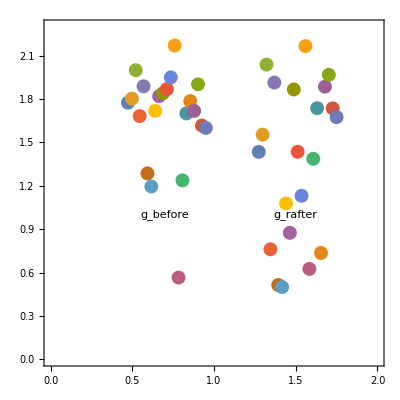

```mathematica
Clear[MakePoints]
colors=Join[ColorData[97,"ColorList"],ColorData[98,"ColorList"]]
MakePoints[x_,data_]:={AbsolutePointSize[10],Table[{colors[[i]],Point[{x+(i/Length[data]-0.5)0.5,data[[i]]}]},{i,Length[data]}]};
Graphics[{MakePoints[0.7,LBrates],MakePoints[1.5,RIFrates]},Epilog->{Text["g_before",{0.7,1.0}],Text["g_rafter",{1.5,1.0}]},Axes->{None,Automatic},PlotRange->{{0,2},{0.,2.3}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,300}]
```

```mathematica
mutantorigin=Import["mutation_summary_turbidostat.xlsx","XLSX"][[1,2;;]];
mutantgrowthrates=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1,2;;]];
nosdetected=mutantorigin[[Position[mutantorigin,#][[1,1]]]][[2;;3]]&/@mutantgrowthrates[[4;;,3]]
RIFratesTurbidostat=Select[Table[If[nosdetected[[i,2]]>0,RIFrates[[i]],0],{i,21}],(#>0)&]
LBratesTurbidostat=Select[Table[If[nosdetected[[i,2]]>0,LBrates[[i]],0],{i,21}],(#>0)&]
```

{{2.,1.},{2.,0.},{1.,1.},{4.,0.},{3.,2.},{1.,0.},{2.,0.},{1.,0.},{1.,0.},{2.,2.},{2.,1.},{1.,0.},{1.,1.},{1.,0.},{2.,0.},{1.,1.},{1.,0.},{0.,1.},{0.,1.},{0.,1.},{0.,1.}}

{1.43415,2.03764,1.91346,1.86566,1.43485,2.16552,1.73611,1.88525,1.96703,1.73519,1.6746}

{1.77465,1.99908,1.88764,1.84011,1.86841,2.16938,1.70002,1.71756,1.90167,1.6161,1.59997}

#### Color code : magenta = found in the bioreactor and in the plate, yellow = only on the plate, red = only in the bioreactor

```mathematica
colors=Table[If[nosdetected[[i,1]]>0,If[nosdetected[[i,2]]>0,Magenta,Darker[Yellow]],Red],{i,21}]
```

{RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 1],RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 1],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

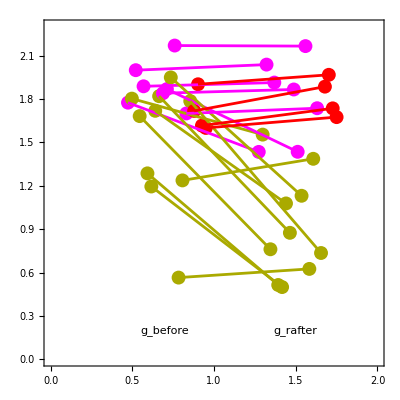

```mathematica
Show[Graphics[{MakePoints[0.7,LBrates],MakePoints[1.5,RIFrates]},Epilog->{Text["g_before",{0.7,0.2}],Text["g_rafter",{1.5,0.2}]},Axes->{None,Automatic},PlotRange->{{0,2},{0.,2.3}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,300}],ListPlot[Table[{{0.7+(i/21-0.5)0.5,LBrates[[i]]},{1.5+(i/21-0.5)0.5,RIFrates[[i]]}},{i,21}],Joined->True,PlotRange->All,PlotStyle->colors]]
```

### Run the model:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult"]

args=Table[
{"fixed_mu_2strains_mult_mutants_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]


SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 23 13 fixed_mu_2strains_mult_mutants_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1 fixed_mu_2strains_mult_mutants_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1 fixed_mu_2strains_mult_mutants_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1 fixed_mu_2strains_mult_mutants_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1 fixed_mu_2strains_mult_mutants_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1 fixed_mu_2strains_mult_mutants_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1 fixed_mu_2strains_mult_mutants_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1 fixed_mu_2strains_mult_mutants_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1 fixed_mu_2strains_mult_mutants_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1 fixed_mu_2strains_mult_mutants_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1 fixed_mu_2strains_mult_mutants_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1 fixed_mu_2strains_mult_mutants_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1 fixed_mu_2strains_mult_mutants_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1 fixed_mu_2strains_mult_mutants_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1 fixed_mu_2strains_mult_mutants_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1 fixed_mu_2strains_mult_mutants_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1 fixed_mu_2strains_mult_mutants_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_17.dat  0.1 fixed_mu_2strains_mult_mutants_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_18.dat  0.1 fixed_mu_2strains_mult_mutants_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_19.dat  0.1 fixed_mu_2strains_mult_mutants_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_20.dat  0.1 fixed_mu_2strains_mult_mutants_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_21.dat  0.1 fixed_mu_2strains_mult_mutants_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_22.dat  0.1 fixed_mu_2strains_mult_mutants_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_23.dat  0.1

0

0.945522

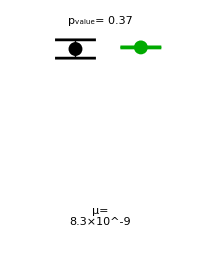

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_no_lag_Pregrowth.png

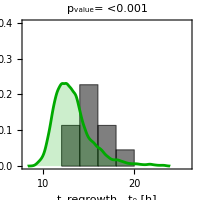

KS-test p-value: 4.90579×10^-6

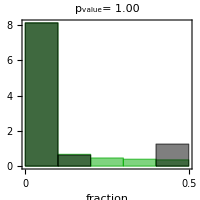

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.812071

```mathematica
simdist=Table[Import["models\\RIF_mult\\distribution_fixed_mu_2strains_mult_mutants_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["RIF_mult_allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["RIF_mult_allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["RIF_mult_allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
{vols2,births2,odinis2,tfirstthr2,tends2}=paramsRIFshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
```

16

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;
alleles=Length[LBrates];
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

8.3×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult"]

args=Table[
{"preexist_res_2strains_mult_alleles_"<>mutrate<>"_RIF"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1 "},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 16 13 preexist_res_2strains_mult_alleles_8.3e-9_RIF1 25.19 0.00398153 100 4.465 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF2 24.93 0.00349311 100 4.46503 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF3 24.01 0.00435082 100 4.46511 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF4 26.48 0.00390985 100 4.46514 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF5 25.41 0.00108037 100 5.614 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF6 24.82 0.000859569 100 5.61403 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF7 24.95 0.000998523 100 5.61408 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF8 26.22 0.000831875 100 5.61414 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF9 26.08 0.00502178 100 4.43167 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF10 24.92 0.0042102 100 4.43172 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF11 24.47 0.00456304 100 4.43178 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF12 25.58 0.004318 100 4.43183 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF13 25.28 0.00598778 100 4.39206 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF14 25.43 0.00487188 100 4.39211 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF15 24.44 0.00556088 100 4.39217 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1  preexist_res_2strains_mult_alleles_8.3e-9_RIF16 25.86 0.00500046 100 4.39222 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1

0

16

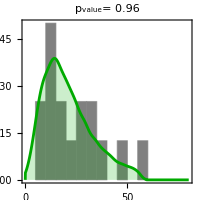

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\RIF_mult\\strains_preexist_res_2strains_mult_alleles_"<>mutrate<>"_RIF",strains,alleles,NotebookDirectory[]<>"\\figures\\RIF_mult_allele_no_lag_Nmut.png"]
```

## Optimize μ to get the best fit to CFUs:

```mathematica
Clear[RunOnceMultNoLag]
RunOnceMultNoLag[mu_]:=RunOnceMultNoLag[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult"];
args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2]," 100 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1 "},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)
(*Run["powershell -NoExit "<>name];*);
simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",Table[Number,{strains (alleles+1)}]],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus];
Return[-pval]]
```

```mathematica
RunOnceMultNoLag[1 10^-8]
```

-0.357953

```mathematica
NaiveMinimization[RunOnceMultNoLag,5 10^-9,3 10^-8,10^-10]
```

5.×10^-9 2.04508×10^-8 fa=-0.00259421 fb=-3.41458×10^-8

5.×10^-9 1.45492×10^-8 fa=-0.172447 fb=-0.00259421

5.×10^-9 1.09017×10^-8 fa=-0.88853 fb=-0.172447

7.25425×10^-9 1.09017×10^-8 fa=-0.53301 fb=-0.172447

7.25425×10^-9 9.5085×10^-9 fa=-0.88853 fb=-0.528928

8.11529×10^-9 9.5085×10^-9 fa=-0.880055 fb=-0.528928

8.11529×10^-9 8.97634×10^-9 fa=-0.88853 fb=-0.780087

8.11529×10^-9 8.64745×10^-9 fa=-0.965492 fb=-0.88853

8.11529×10^-9 8.44419×10^-9 fa=-0.974721 fb=-0.965492

8.24092×10^-9 8.44419×10^-9 fa=-0.96128 fb=-0.965492

8.34255×10^-9

## Multi-allele model for RIF. Different mutation probabilities. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
mutexpfreqs=Import["RpoB_SNP_summary.xlsx"][[1]][[4;;,{2,5}]]
```

{{Q148L,0.07},{R454P,0.07},{S512P,0.21},{S512F,0.35},{Q513L,0.07},{Q513P,0.16},{D516G,0.21},{D516Y,0.13},{H526Y,0.35},{H526L,0.07},{H526D,0.07},{H526N,0.13},{R529C,0.35},{S531F,0.35},{S531Y,0.13},{G534V,0.13},{G534D,0.35},{T563P,0.16},{P564R,0.35},{I572S,0.16},{I572L,0.16}}

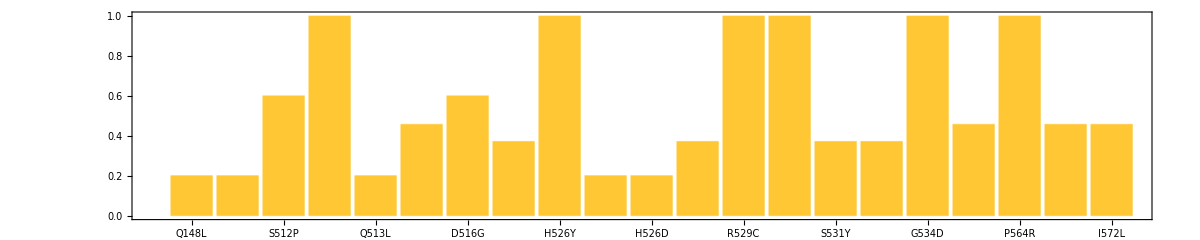

```mathematica
BarChart[mutexpfreqs[[All,2]]/0.35,ChartLabels->mutexpfreqs[[All,1]],AspectRatio->0.2,ImageSize->1200,BaseStyle->FontSize->12]
```

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]
LBrates=allrates[[All,2]];
RIFrates=allrates[[All,3]];

mutprobs={#[[1]],mutexpfreqs[[Position[mutexpfreqs[[All,1]],#[[1]]][[1,1]],2]]}&/@allrates;
DumpSave[NotebookDirectory[]<>"\\RIF_mult_alleles_probs.mx",mutprobs]

LBrates
RIFrates

mutrate="8.3e-9";  (* this value must be the same as for the model with different alleles but no lag, and equal probabilities *)
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]


BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};

Export[NotebookDirectory[]<>"\\models\\RIF_mult_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]]
```

{{S512P,1.77465,1.43415},{S512F,1.80241,1.5536},{D516Y,1.99908,2.03764},{T563P,1.68159,0.76101},{H526Y,1.88764,1.91346},{G534D,1.28577,0.513987},{R454P,1.19505,0.499673},{I572L,1.71817,1.07787},{Q148L,1.81943,0.874744},{H526D,1.84011,1.86566},{D516G,1.86841,1.43485},{I572S,1.9491,1.13081},{H526L,2.16938,2.16552},{R529C,0.565199,0.625219},{Q513P,1.23712,1.38641},{S531F,1.70002,1.73611},{G534V,1.78559,0.735189},{Q513L,1.71756,1.88525},{H526N,1.90167,1.96703},{S531Y,1.6161,1.73519},{P564R,1.59997,1.6746}}

{{{S512P,0.21},{S512F,0.35},{D516Y,0.13},{T563P,0.16},{H526Y,0.35},{G534D,0.35},{R454P,0.07},{I572L,0.16},{Q148L,0.07},{H526D,0.07},{D516G,0.21},{I572S,0.16},{H526L,0.07},{R529C,0.35},{Q513P,0.16},{S531F,0.35},{G534V,0.13},{Q513L,0.07},{H526N,0.13},{S531Y,0.13},{P564R,0.35}}}

{1.77465,1.80241,1.99908,1.68159,1.88764,1.28577,1.19505,1.71817,1.81943,1.84011,1.86841,1.9491,2.16938,0.565199,1.23712,1.70002,1.78559,1.71756,1.90167,1.6161,1.59997}

{1.43415,1.5536,2.03764,0.76101,1.91346,0.513987,0.499673,1.07787,0.874744,1.86566,1.43485,1.13081,2.16552,0.625219,1.38641,1.73611,0.735189,1.88525,1.96703,1.73519,1.6746}

8.3×10^-9

2

21

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_diffp"]

args=Table[
{"fixed_mu_2strains_mult_mutants_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params_v2.exe 23 13 fixed_mu_2strains_mult_mutants_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1 fixed_mu_2strains_mult_mutants_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1 fixed_mu_2strains_mult_mutants_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1 fixed_mu_2strains_mult_mutants_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1 fixed_mu_2strains_mult_mutants_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1 fixed_mu_2strains_mult_mutants_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1 fixed_mu_2strains_mult_mutants_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1 fixed_mu_2strains_mult_mutants_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1 fixed_mu_2strains_mult_mutants_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1 fixed_mu_2strains_mult_mutants_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1 fixed_mu_2strains_mult_mutants_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1 fixed_mu_2strains_mult_mutants_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1 fixed_mu_2strains_mult_mutants_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1 fixed_mu_2strains_mult_mutants_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1 fixed_mu_2strains_mult_mutants_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1 fixed_mu_2strains_mult_mutants_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1 fixed_mu_2strains_mult_mutants_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_17.dat  0.1 fixed_mu_2strains_mult_mutants_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_18.dat  0.1 fixed_mu_2strains_mult_mutants_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_19.dat  0.1 fixed_mu_2strains_mult_mutants_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_20.dat  0.1 fixed_mu_2strains_mult_mutants_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_21.dat  0.1 fixed_mu_2strains_mult_mutants_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_22.dat  0.1 fixed_mu_2strains_mult_mutants_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_23.dat  0.1

0

0.940535

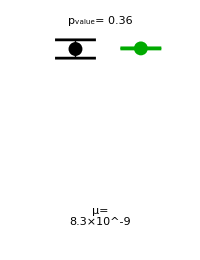

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_no_lag_diffP_Pregrowth.png

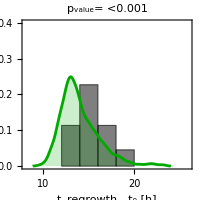

KS-test p-value: 0.000809718

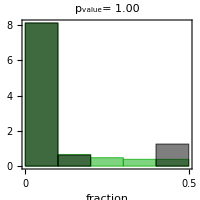

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.809387

```mathematica
simdist=Table[Import["models\\RIF_mult_diffp\\distribution_fixed_mu_2strains_mult_mutants_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["RIF_mult_allele_no_lag_diffP_Pregrowth.png"]
RegrowtTimeDistribution["RIF_mult_allele_no_lag_diffP_Tregrowth.png"]
LeastAbundantStrain["RIF_mult_allele_no_lag_diffP_LBS.png"]
```

## Phenotypic lag model for RIF. Many resistant alleles. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]

LBrates=allrates[[All,2]];
RIFrates=allrates[[All,3]];

mutprobs={#[[1]],1}&/@allrates[[All]]  (* same mutation probs for all alleles *)

LBrates
RIFrates

mutrate="8.3e-9";  (* this value must be the same as for the model with different alleles but no lag, and equal probabilities *)
lagrate="0.02" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.8; (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction RIFrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{S512P,1.77465,1.43415},{S512F,1.80241,1.5536},{D516Y,1.99908,2.03764},{T563P,1.68159,0.76101},{H526Y,1.88764,1.91346},{G534D,1.28577,0.513987},{R454P,1.19505,0.499673},{I572L,1.71817,1.07787},{Q148L,1.81943,0.874744},{H526D,1.84011,1.86566},{D516G,1.86841,1.43485},{I572S,1.9491,1.13081},{H526L,2.16938,2.16552},{R529C,0.565199,0.625219},{Q513P,1.23712,1.38641},{S531F,1.70002,1.73611},{G534V,1.78559,0.735189},{Q513L,1.71756,1.88525},{H526N,1.90167,1.96703},{S531Y,1.6161,1.73519},{P564R,1.59997,1.6746}}

{{S512P,1},{S512F,1},{D516Y,1},{T563P,1},{H526Y,1},{G534D,1},{R454P,1},{I572L,1},{Q148L,1},{H526D,1},{D516G,1},{I572S,1},{H526L,1},{R529C,1},{Q513P,1},{S531F,1},{G534V,1},{Q513L,1},{H526N,1},{S531Y,1},{P564R,1}}

{1.77465,1.80241,1.99908,1.68159,1.88764,1.28577,1.19505,1.71817,1.81943,1.84011,1.86841,1.9491,2.16938,0.565199,1.23712,1.70002,1.78559,1.71756,1.90167,1.6161,1.59997}

{1.43415,1.5536,2.03764,0.76101,1.91346,0.513987,0.499673,1.07787,0.874744,1.86566,1.43485,1.13081,2.16552,0.625219,1.38641,1.73611,0.735189,1.88525,1.96703,1.73519,1.6746}

8.3×10^-9

2

21

```mathematica
Sort[Flatten[wt]]
Sort[Flatten[it]]
Sort[Flatten[mt]]
```

{0,0,2.00363,2.00363}

{0.399738,0.399738,0.41119,0.41119,0.500175,0.500175,0.565199,0.565199,0.588151,0.588151,0.608808,0.608808,0.699795,0.699795,0.862296,0.862296,0.904648,0.904648,1.10913,1.10913,1.14732,1.14732,1.14788,1.14788,1.19505,1.19505,1.23712,1.23712,1.24288,1.24288,1.28577,1.28577,1.33968,1.33968,1.38815,1.38815,1.38889,1.38889,1.49253,1.49253,1.5082,1.5082,1.53077,1.53077,1.57362,1.57362,1.59997,1.59997,1.6161,1.6161,1.63011,1.63011,1.68159,1.68159,1.70002,1.70002,1.71756,1.71756,1.71817,1.71817,1.73242,1.73242,1.77465,1.77465,1.78559,1.78559,1.80241,1.80241,1.81943,1.81943,1.84011,1.84011,1.86841,1.86841,1.88764,1.88764,1.90167,1.90167,1.9491,1.9491,1.99908,1.99908,2.16938,2.16938}

{0.499673,0.499673,0.513987,0.513987,0.565199,0.565199,0.625219,0.625219,0.735189,0.735189,0.76101,0.76101,0.874744,0.874744,1.07787,1.07787,1.13081,1.13081,1.19505,1.19505,1.23712,1.23712,1.28577,1.28577,1.38641,1.38641,1.43415,1.43415,1.43485,1.43485,1.5536,1.5536,1.59997,1.59997,1.6161,1.6161,1.6746,1.6746,1.68159,1.68159,1.70002,1.70002,1.71756,1.71756,1.71817,1.71817,1.73519,1.73519,1.73611,1.73611,1.77465,1.77465,1.78559,1.78559,1.80241,1.80241,1.81943,1.81943,1.84011,1.84011,1.86566,1.86566,1.86841,1.86841,1.88525,1.88525,1.88764,1.88764,1.90167,1.90167,1.91346,1.91346,1.9491,1.9491,1.96703,1.96703,1.99908,1.99908,2.03764,2.03764,2.16552,2.16552,2.16938,2.16938}

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag"]

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate (* tolerance, omega *)},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]


SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 23 14 fixed_mu_mult_strains_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1  0.02 fixed_mu_mult_strains_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1  0.02 fixed_mu_mult_strains_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1  0.02 fixed_mu_mult_strains_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1  0.02 fixed_mu_mult_strains_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1  0.02 fixed_mu_mult_strains_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1  0.02 fixed_mu_mult_strains_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1  0.02 fixed_mu_mult_strains_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1  0.02 fixed_mu_mult_strains_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1  0.02 fixed_mu_mult_strains_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1  0.02 fixed_mu_mult_strains_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1  0.02 fixed_mu_mult_strains_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1  0.02 fixed_mu_mult_strains_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1  0.02 fixed_mu_mult_strains_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1  0.02 fixed_mu_mult_strains_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1  0.02 fixed_mu_mult_strains_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1  0.02 fixed_mu_mult_strains_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_17.dat  0.1  0.02 fixed_mu_mult_strains_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_18.dat  0.1  0.02 fixed_mu_mult_strains_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_19.dat  0.1  0.02 fixed_mu_mult_strains_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_20.dat  0.1  0.02 fixed_mu_mult_strains_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_21.dat  0.1  0.02 fixed_mu_mult_strains_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_22.dat  0.1  0.02 fixed_mu_mult_strains_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_23.dat  0.1  0.02

0

0.903464

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_params.png

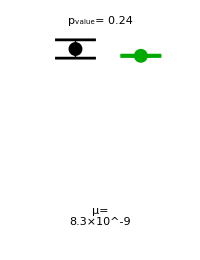

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_Pregrowth.png

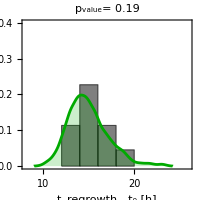

KS-test p-value: 0.191036

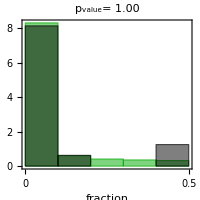

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.829967

```mathematica
simdist=Table[Import["models\\RIF_mult_lag\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\RIF_mult_allele_lag_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["RIF_mult_allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["RIF_mult_allele_lag_Tregrowth.png"]
LeastAbundantStrain["RIF_mult_allele_lag_LBS.png"]
```

### Find optimal parameters:

```mathematica
Clear[RunOnce2,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce2[ω_?NumericQ,q_?NumericQ]:=RunOnce2[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
strains=2;alleles=Length[LBrates];
mutprobs={#[[1]],1}&/@allrates[[All]]  ;(* same mutation probs for all alleles *)
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[Abs[q] RIFrates[[i]],{strains}],{i,alleles}]]};
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}];
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth]," 300 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",ToString[Abs[ω]](* tolerance, omega *)},{nn,Length[births]}]; (* tolerance, omega *)

name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];

ret=RunProcess[{"powershell",name}];

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\RIF_mult_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

8.3×10^-9

```mathematica
RunOnce2[0.05,0.5]
```

ω= 0.05 q =0.5 fun=-0.0662942

-0.0662942

```mathematica
fits=Table[{ω,q,RunOnce2[ω,q]},{ω,0.01,0.03,0.005},{q,0.4,0.9,0.1}]
```

ω= 0.01 q =0.4 fun=19.3484

ω= 0.01 q =0.5 fun=9.68699

ω= 0.01 q =0.6 fun=6.78775

ω= 0.01 q =0.7 fun=-0.0564408

ω= 0.01 q =0.8 fun=-0.19673

ω= 0.01 q =0.9 fun=7.18573

ω= 0.015 q =0.4 fun=17.508

ω= 0.015 q =0.5 fun=6.3507

ω= 0.015 q =0.6 fun=-0.0280017

ω= 0.015 q =0.7 fun=-0.107455

ω= 0.015 q =0.8 fun=-0.193774

ω= 0.015 q =0.9 fun=8.70609

ω= 0.02 q =0.4 fun=10.5423

ω= 0.02 q =0.5 fun=-0.00620673

ω= 0.02 q =0.6 fun=-0.0412987

ω= 0.02 q =0.7 fun=-0.137585

ω= 0.02 q =0.8 fun=-0.277314

ω= 0.02 q =0.9 fun=9.33146

ω= 0.025 q =0.4 fun=8.23785

ω= 0.025 q =0.5 fun=-0.00818083

ω= 0.025 q =0.6 fun=-0.0610272

ω= 0.025 q =0.7 fun=-0.174903

ω= 0.025 q =0.8 fun=-0.116929

ω= 0.025 q =0.9 fun=9.53988

ω= 0.03 q =0.4 fun=7.04285

ω= 0.03 q =0.5 fun=-0.0211219

ω= 0.03 q =0.6 fun=-0.09033

ω= 0.03 q =0.7 fun=-0.165863

ω= 0.03 q =0.8 fun=6.44248

ω= 0.03 q =0.9 fun=9.59208

{{{0.01,0.4,19.3484},{0.01,0.5,9.68699},{0.01,0.6,6.78775},{0.01,0.7,-0.0564408},{0.01,0.8,-0.19673},{0.01,0.9,7.18573}},{{0.015,0.4,17.508},{0.015,0.5,6.3507},{0.015,0.6,-0.0280017},{0.015,0.7,-0.107455},{0.015,0.8,-0.193774},{0.015,0.9,8.70609}},{{0.02,0.4,10.5423},{0.02,0.5,-0.00620673},{0.02,0.6,-0.0412987},{0.02,0.7,-0.137585},{0.02,0.8,-0.277314},{0.02,0.9,9.33146}},{{0.025,0.4,8.23785},{0.025,0.5,-0.00818083},{0.025,0.6,-0.0610272},{0.025,0.7,-0.174903},{0.025,0.8,-0.116929},{0.025,0.9,9.53988}},{{0.03,0.4,7.04285},{0.03,0.5,-0.0211219},{0.03,0.6,-0.09033},{0.03,0.7,-0.165863},{0.03,0.8,6.44248},{0.03,0.9,9.59208}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.02,0.8,-0.277314},{0.01,0.8,-0.19673},{0.015,0.8,-0.193774},{0.025,0.7,-0.174903},{0.03,0.7,-0.165863},{0.02,0.7,-0.137585},{0.025,0.8,-0.116929},{0.015,0.7,-0.107455},{0.03,0.6,-0.09033},{0.025,0.6,-0.0610272},{0.01,0.7,-0.0564408},{0.02,0.6,-0.0412987},{0.015,0.6,-0.0280017},{0.03,0.5,-0.0211219},{0.025,0.5,-0.00818083},{0.02,0.5,-0.00620673},{0.015,0.5,6.3507},{0.03,0.8,6.44248},{0.01,0.6,6.78775},{0.03,0.4,7.04285},{0.01,0.9,7.18573},{0.025,0.4,8.23785},{0.015,0.9,8.70609},{0.02,0.9,9.33146},{0.025,0.9,9.53988},{0.03,0.9,9.59208},{0.01,0.5,9.68699},{0.02,0.4,10.5423},{0.015,0.4,17.508},{0.01,0.4,19.3484}}

```mathematica
ListDensityPlot[Flatten[fits,1],PlotRange->{All,-0.05}]
```

-Graphics-

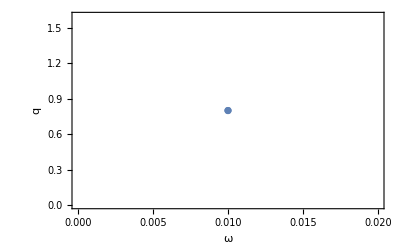

```mathematica
ListPlot[Select[Flatten[fits,1],(#[[3]]<-0.05)&][[All,{1,2}]],BaseStyle->FontSize->12,FrameLabel->{"ω","q"}]
```

### Short - term experiment :

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births2[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction RIFrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

8.3×10^-9

2

21

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag"]

args=Table[
{"preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_RIF"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate (* tolerance, omega *)},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 16 14 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF1 25.19 0.00398153 100 4.465 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF2 24.93 0.00349311 100 4.46503 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF3 24.01 0.00435082 100 4.46511 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF4 26.48 0.00390985 100 4.46514 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF5 25.41 0.00108037 100 5.614 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF6 24.82 0.000859569 100 5.61403 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF7 24.95 0.000998523 100 5.61408 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF8 26.22 0.000831875 100 5.61414 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF9 26.08 0.00502178 100 4.43167 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF10 24.92 0.0042102 100 4.43172 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF11 24.47 0.00456304 100 4.43178 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF12 25.58 0.004318 100 4.43183 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF13 25.28 0.00598778 100 4.39206 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF14 25.43 0.00487188 100 4.39211 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF15 24.44 0.00556088 100 4.39217 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1  0.02 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF16 25.86 0.00500046 100 4.39222 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1  0.02

0

16

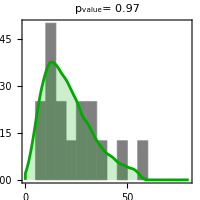

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\RIF_mult_lag\\strains_preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_RIF",strains,2alleles,NotebookDirectory[]<>"\\figures\\RIF_mult_allele_lag_Nmut.png"]
```

## Phenotypic lag model for RIF. Many resistant alleles. Different mutation probabilities. Mixed strains AD30 and AD30YFP .

### Long - term experiment

```mathematica
mutexpfreqs=Import["RpoB_SNP_summary.xlsx"][[1]][[4;;,{2,5}]]
```

{{Q148L,0.07},{R454P,0.07},{S512P,0.21},{S512F,0.35},{Q513L,0.07},{Q513P,0.16},{D516G,0.21},{D516Y,0.13},{H526Y,0.35},{H526L,0.07},{H526D,0.07},{H526N,0.13},{R529C,0.35},{S531F,0.35},{S531Y,0.13},{G534V,0.13},{G534D,0.35},{T563P,0.16},{P564R,0.35},{I572S,0.16},{I572L,0.16}}

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];

allrates={#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&]

LBrates=allrates[[All,2]]
RIFrates=allrates[[All,3]]

mutprobs={#[[1]],mutexpfreqs[[Position[mutexpfreqs[[All,1]],#[[1]]][[1,1]],2]]}&/@allrates

LBrates
RIFrates

mutrate="8.3e-9";  (* this value must be the same as for all models with lag *)
lagrate="0.025" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.9; (* this must be experimentally chosen to give the best fit *)

mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction RIFrates[[i]],{strains}],{i,alleles}]]};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}]
```

{{S512P,1.77465,1.43415},{S512F,1.80241,1.5536},{D516Y,1.99908,2.03764},{T563P,1.68159,0.76101},{H526Y,1.88764,1.91346},{G534D,1.28577,0.513987},{R454P,1.19505,0.499673},{I572L,1.71817,1.07787},{Q148L,1.81943,0.874744},{H526D,1.84011,1.86566},{D516G,1.86841,1.43485},{I572S,1.9491,1.13081},{H526L,2.16938,2.16552},{R529C,0.565199,0.625219},{Q513P,1.23712,1.38641},{S531F,1.70002,1.73611},{G534V,1.78559,0.735189},{Q513L,1.71756,1.88525},{H526N,1.90167,1.96703},{S531Y,1.6161,1.73519},{P564R,1.59997,1.6746}}

{1.77465,1.80241,1.99908,1.68159,1.88764,1.28577,1.19505,1.71817,1.81943,1.84011,1.86841,1.9491,2.16938,0.565199,1.23712,1.70002,1.78559,1.71756,1.90167,1.6161,1.59997}

{1.43415,1.5536,2.03764,0.76101,1.91346,0.513987,0.499673,1.07787,0.874744,1.86566,1.43485,1.13081,2.16552,0.625219,1.38641,1.73611,0.735189,1.88525,1.96703,1.73519,1.6746}

{{S512P,0.21},{S512F,0.35},{D516Y,0.13},{T563P,0.16},{H526Y,0.35},{G534D,0.35},{R454P,0.07},{I572L,0.16},{Q148L,0.07},{H526D,0.07},{D516G,0.21},{I572S,0.16},{H526L,0.07},{R529C,0.35},{Q513P,0.16},{S531F,0.35},{G534V,0.13},{Q513L,0.07},{H526N,0.13},{S531Y,0.13},{P564R,0.35}}

{1.77465,1.80241,1.99908,1.68159,1.88764,1.28577,1.19505,1.71817,1.81943,1.84011,1.86841,1.9491,2.16938,0.565199,1.23712,1.70002,1.78559,1.71756,1.90167,1.6161,1.59997}

{1.43415,1.5536,2.03764,0.76101,1.91346,0.513987,0.499673,1.07787,0.874744,1.86566,1.43485,1.13081,2.16552,0.625219,1.38641,1.73611,0.735189,1.88525,1.96703,1.73519,1.6746}

8.3×10^-9

2

21

```mathematica
Sort[Flatten[wt]]
Sort[Flatten[it]]
Sort[Flatten[mt]]
```

{0,0,2.00363,2.00363}

{0.449706,0.449706,0.462588,0.462588,0.562697,0.562697,0.565199,0.565199,0.66167,0.66167,0.684909,0.684909,0.78727,0.78727,0.970083,0.970083,1.01773,1.01773,1.19505,1.19505,1.23712,1.23712,1.24777,1.24777,1.28577,1.28577,1.29073,1.29073,1.29137,1.29137,1.39824,1.39824,1.50714,1.50714,1.56167,1.56167,1.5625,1.5625,1.59997,1.59997,1.6161,1.6161,1.67909,1.67909,1.68159,1.68159,1.69673,1.69673,1.70002,1.70002,1.71756,1.71756,1.71817,1.71817,1.72211,1.72211,1.77033,1.77033,1.77465,1.77465,1.78559,1.78559,1.80241,1.80241,1.81943,1.81943,1.83388,1.83388,1.84011,1.84011,1.86841,1.86841,1.88764,1.88764,1.90167,1.90167,1.94897,1.94897,1.9491,1.9491,1.99908,1.99908,2.16938,2.16938}

{0.499673,0.499673,0.513987,0.513987,0.565199,0.565199,0.625219,0.625219,0.735189,0.735189,0.76101,0.76101,0.874744,0.874744,1.07787,1.07787,1.13081,1.13081,1.19505,1.19505,1.23712,1.23712,1.28577,1.28577,1.38641,1.38641,1.43415,1.43415,1.43485,1.43485,1.5536,1.5536,1.59997,1.59997,1.6161,1.6161,1.6746,1.6746,1.68159,1.68159,1.70002,1.70002,1.71756,1.71756,1.71817,1.71817,1.73519,1.73519,1.73611,1.73611,1.77465,1.77465,1.78559,1.78559,1.80241,1.80241,1.81943,1.81943,1.84011,1.84011,1.86566,1.86566,1.86841,1.86841,1.88525,1.88525,1.88764,1.88764,1.90167,1.90167,1.91346,1.91346,1.9491,1.9491,1.96703,1.96703,1.99908,1.99908,2.03764,2.03764,2.16552,2.16552,2.16938,2.16938}

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp"]

args=Table[
{"fixed_mu_mult_strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate (* tolerance, omega *)},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult_lag_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 23 14 fixed_mu_mult_strains_1 24.74 0.00464461 4.50619 24.266 20.8342 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1  0.025 fixed_mu_mult_strains_2 26.23 0.00400177 4.47525 24.266 21.3245 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1  0.025 fixed_mu_mult_strains_3 24.14 0.00412012 4.60053 24.266 19.9152 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1  0.025 fixed_mu_mult_strains_4 25.32 0.00448428 4.56925 24.266 20.4595 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1  0.025 fixed_mu_mult_strains_5 25.07 0.00515094 4.55311 23.6529 19.2623 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1  0.025 fixed_mu_mult_strains_6 26.29 0.00412982 4.48311 23.653 16.8407 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1  0.025 fixed_mu_mult_strains_7 24.14 0.00376088 4.51594 23.653 17.8823 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1  0.025 fixed_mu_mult_strains_8 25.85 0.0044634 4.61958 23.653 18.3482 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1  0.025 fixed_mu_mult_strains_9 25.17 0.00256188 4.92619 28.4731 19.7233 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1  0.025 fixed_mu_mult_strains_10 24.94 0.00225436 5.38022 28.4731 21.9101 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1  0.025 fixed_mu_mult_strains_11 25.55 0.00266147 5.03167 28.4733 21.8856 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1  0.025 fixed_mu_mult_strains_12 24.9 0.0050119 4.54533 24.2488 19.8833 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1  0.025 fixed_mu_mult_strains_13 25.3 0.00468726 4.59394 24.2488 19.8376 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1  0.025 fixed_mu_mult_strains_14 24.88 0.00431979 4.77936 24.2488 19.4321 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1  0.025 fixed_mu_mult_strains_15 25.56 0.00434558 4.51489 24.2488 22.3032 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1  0.025 fixed_mu_mult_strains_16 25.42 0.00266369 4.81117 28.2667 20.0353 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1  0.025 fixed_mu_mult_strains_17 24.79 0.00191899 4.90753 28.2667 24.7578 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_17.dat  0.1  0.025 fixed_mu_mult_strains_18 24.77 0.00281276 4.49742 28.2669 35 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_18.dat  0.1  0.025 fixed_mu_mult_strains_19 26.15 0.00204638 4.45014 28.2669 17.3008 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_19.dat  0.1  0.025 fixed_mu_mult_strains_20 25.1 0.045956 2.85561 26.0128 17.1475 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_20.dat  0.1  0.025 fixed_mu_mult_strains_21 25.48 0.0379229 2.93222 26.0128 21.71 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_21.dat  0.1  0.025 fixed_mu_mult_strains_22 24.14 0.0597045 2.49257 26.0128 14.9319 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_22.dat  0.1  0.025 fixed_mu_mult_strains_23 26.14 0.0258444 2.98017 26.0129 18.3095 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_23.dat  0.1  0.025

0

0.920432

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_diffp_params.png

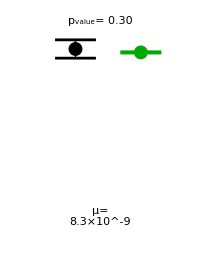

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_diffP_Pregrowth.png

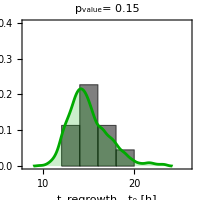

KS-test p-value: 0.14993

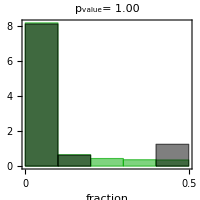

fraction below 0.1 (exp):0.8125

fraction below 0.1 (sim):0.819077

```mathematica
simdist=Table[Import["models\\RIF_mult_lag_diffp\\distribution_fixed_mu_mult_strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

Export[NotebookDirectory[]<>"\\figures\\RIF_mult_allele_lag_diffp_params.png",Style["ω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
RegrowthProbPlot["RIF_mult_allele_lag_diffP_Pregrowth.png"]
RegrowtTimeDistribution["RIF_mult_allele_lag_diffP_Tregrowth.png"]
LeastAbundantStrain["RIF_mult_allele_lag_diffP_LBS.png"]
```

### Optimize parameters:

```mathematica
Clear[RunOnce3,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce3[ω_?NumericQ,q_?NumericQ]:=RunOnce3[ω,q]=Module[{pval1,pval2,pval3,simcfus,simdist,tmp,psurv,psurvexp,ret,processes,fractions},
(*Return[ω^2+q^2]*)
strains=2;alleles=Length[LBrates];
mutprobs={#[[1]],mutexpfreqs[[Position[mutexpfreqs[[All,1]],#[[1]]][[1,1]],2]]}&/@allrates ;
Do[
wt={Table[births[[nn,1]],{i,strains}],Table[0,{i,strains}]};
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[Abs[q] RIFrates[[i]],{strains}],{i,alleles}]]};
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols]}];
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth]," 100 ",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",ToString[Abs[ω]](* tolerance, omega *)},{nn,Length[births]}]; (* tolerance, omega *)

name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];

ret=RunProcess[{"powershell",name}];


SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\RIF_mult_lag_diffp\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
(*pval2=Mean[Table[KolmogorovSmirnovTest[RandomSample[Select[tmp⟦All,2⟧,NumberQ[#1]&],Length[tregrowths]],Select[tregrowths-ainjs,NumberQ[#1]&]],{Ceiling[Length[tmp]/Length[tregrowths]]}]](* average p-value for ks-test on samples of the same length *);*)
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q," pvals=",{pval1,pval2,pval3}, " fun=",ret];
Return[ret]
]
```

8.3×10^-9

```mathematica
RunOnce3[0.0203,0.8]
```

ω= 0.0203 q =0.8 pvals={0.122852,0.434879,0.861661} fun=-0.122852

-0.122852

```mathematica
fits=Table[{ω,q,RunOnce3[ω,q]},{ω,0.01,0.025,0.005},{q,0.5,0.9,0.1}]
```

ω= 0.01 q =0.5 pvals={0.0000182867,0.000302525,0.0777062} fun=12.1991

ω= 0.01 q =0.6 pvals={0.00181368,0.000351213,0.458488} fun=9.96306

ω= 0.01 q =0.7 pvals={0.0374531,0.00418529,0.761951} fun=9.54402

ω= 0.01 q =0.8 pvals={0.0740397,0.0696785,0.823912} fun=2.95811

ω= 0.01 q =0.9 pvals={0.312405,0.687553,0.874012} fun=-0.312405

ω= 0.015 q =0.5 pvals={0.000271628,0.0031207,0.179363} fun=9.68766

ω= 0.015 q =0.6 pvals={0.00948147,0.00972579,0.420861} fun=9.01794

ω= 0.015 q =0.7 pvals={0.0519422,0.0327935,0.713876} fun=6.66871

ω= 0.015 q =0.8 pvals={0.10351,0.4331,0.873435} fun=-0.10351

ω= 0.015 q =0.9 pvals={0.256856,0.362525,0.912441} fun=-0.256856

ω= 0.02 q =0.5 pvals={0.000736652,0.00773477,0.176269} fun=9.22579

ω= 0.02 q =0.6 pvals={0.0134763,0.00756319,0.485627} fun=9.23021

ω= 0.02 q =0.7 pvals={0.108154,0.116383,0.856968} fun=-0.108154

ω= 0.02 q =0.8 pvals={0.17389,0.383036,0.852777} fun=-0.17389

ω= 0.02 q =0.9 pvals={0.250773,0.172477,0.856806} fun=-0.250773

ω= 0.025 q =0.5 pvals={0.00223788,0.0215924,0.19902} fun=7.83852

ω= 0.025 q =0.6 pvals={0.0129976,0.0540777,0.379221} fun=4.57923

ω= 0.025 q =0.7 pvals={0.0896039,0.149168,0.835996} fun=-0.0896039

ω= 0.025 q =0.8 pvals={0.139639,0.841652,0.809014} fun=-0.139639

ω= 0.025 q =0.9 pvals={0.322965,0.140117,0.853178} fun=-0.322965

{{{0.01,0.5,12.1991},{0.01,0.6,9.96306},{0.01,0.7,9.54402},{0.01,0.8,2.95811},{0.01,0.9,-0.312405}},{{0.015,0.5,9.68766},{0.015,0.6,9.01794},{0.015,0.7,6.66871},{0.015,0.8,-0.10351},{0.015,0.9,-0.256856}},{{0.02,0.5,9.22579},{0.02,0.6,9.23021},{0.02,0.7,-0.108154},{0.02,0.8,-0.17389},{0.02,0.9,-0.250773}},{{0.025,0.5,7.83852},{0.025,0.6,4.57923},{0.025,0.7,-0.0896039},{0.025,0.8,-0.139639},{0.025,0.9,-0.322965}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.025,0.9,-0.322965},{0.01,0.9,-0.312405},{0.015,0.9,-0.256856},{0.02,0.9,-0.250773},{0.02,0.8,-0.17389},{0.025,0.8,-0.139639},{0.02,0.7,-0.108154},{0.015,0.8,-0.10351},{0.025,0.7,-0.0896039},{0.01,0.8,2.95811},{0.025,0.6,4.57923},{0.015,0.7,6.66871},{0.025,0.5,7.83852},{0.015,0.6,9.01794},{0.02,0.5,9.22579},{0.02,0.6,9.23021},{0.01,0.7,9.54402},{0.015,0.5,9.68766},{0.01,0.6,9.96306},{0.01,0.5,12.1991}}

### Short - term experiment :

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2
alleles=Length[LBrates]
Do[
(* parent strains before and after the antibiotic *)
wt={Table[births2[[nn,1]],{i,strains}],Table[0,{i,strains}]};
(* intermediate strains before and after the antibiotics*)
it={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[intgrfraction RIFrates[[i]],{strains}],{i,alleles}]]}; (* these rates can be the same as mt rates for this experiment *)
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
Export[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp\\input_params_"<>ToString[nn]<>".dat",Join[{"RIF",RIFlambda,RIF0,strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs[[All,2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

8.3×10^-9

2

21

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp"]

args=Table[
{"preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_RIF"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth2],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate (* tolerance, omega *)},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_mult_lag_diffp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 16 14 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF1 25.19 0.00398153 100 4.465 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_1.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF2 24.93 0.00349311 100 4.46503 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_2.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF3 24.01 0.00435082 100 4.46511 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_3.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF4 26.48 0.00390985 100 4.46514 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_4.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF5 25.41 0.00108037 100 5.614 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_5.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF6 24.82 0.000859569 100 5.61403 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_6.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF7 24.95 0.000998523 100 5.61408 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_7.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF8 26.22 0.000831875 100 5.61414 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_8.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF9 26.08 0.00502178 100 4.43167 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_9.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF10 24.92 0.0042102 100 4.43172 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_10.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF11 24.47 0.00456304 100 4.43178 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_11.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF12 25.58 0.004318 100 4.43183 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_12.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF13 25.28 0.00598778 100 4.39206 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_13.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF14 25.43 0.00487188 100 4.39211 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_14.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF15 24.44 0.00556088 100 4.39217 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_15.dat  0.1  0.025 preexist_res_2strains_mult_allele_lag_8.3e-9_RIF16 25.86 0.00500046 100 4.39222 100 0.05 1000 8.300000000000002e-9 8.300000000000002e-9 0.75 input_params_16.dat  0.1  0.025

0

16

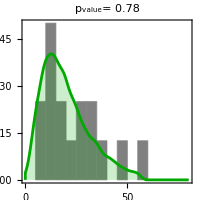

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\RIF_mult_allele_lag_diffp_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\RIF_mult_lag_diffp\\strains_preexist_res_2strains_mult_allele_lag_"<>mutrate<>"_RIF",strains,2alleles,NotebookDirectory[]<>"\\figures\\RIF_mult_allele_lag_diffp_Nmut.png"]
```